```mathematica
Clear["Global`*"];
(*Code from http://flafla2.github.io/2014/08/09/perlinnoise.html*)

(* 3d Perlin Noise defines the OctavePerlin[x, y, z, octaves, persistence] function which gives Perlin3d noise at the position (x,y,z) with a specified number of octaves, and persistence value.  

The function repeats if the world coordinate times the frequency is 256 or greater
e.g. x * frequency = Mod[x * frequency, 256].

*)
```

### 3D Perlin Noise

```mathematica
repeat = -1; (* Set to 5 if we want the world to repeat every 5 units, this method repeats at 256 world units regardless of "repeat" *)

OctavePerlin[x_,y_,z_,octaves_,persistence_] := (
total  =0 ;
frequency = 0.0025;
amplitude = 1;
maxValue = 0;
For[i = 0, i < octaves, i = i +1, 
total +=  perlin[x * frequency, y * frequency, z * frequency] * amplitude;
maxValue += amplitude;
amplitude *= persistence;
frequency *= 2 + 0.02( RandomReal[]-0.5);
];

total/maxValue)

p = {151,160,137,91,90,15,131,13,201,95,96,53,194,233,7,225,140,36,103,30,69,142,8,99,37,240,21,10,23,190,6,148,247,120,234,75,0,26,197,62,94,252,219,203,117,35,11,32,57,177,33,88,237,149,56,87,174,20,125,136,171,168,68,175,74,165,71,134,139,48,27,166,77,146,158,231,83,111,229,122,60,211,133,230,220,105,92,41,55,46,245,40,244,102,143,54,65,25,63,161,1,216,80,73,209,76,132,187,208,89,18,169,200,196,135,130,116,188,159,86,164,100,109,198,173,186,3,64,52,217,226,250,124,123,5,202,38,147,118,126,255,82,85,212,207,206,59,227,47,16,58,17,182,189,28,42,223,183,170,213,119,248,152,2,44,154,163,70,221,153,101,155,167,43,172,9,129,22,39,253,19,98,108,110,79,113,224,232,178,185,112,104,218,246,97,228,251,34,242,193,238,210,144,12,191,179,162,241,81,51,145,235,249,14,239,107,49,192,214,31,181,199,106,157,184,84,204,176,115,121,50,45,127,4,150,254,138,236,205,93,222,114,67,29,24,72,243,141,128,195,78,66,215,61,156,180,

151,160,137,91,90,15,131,13,201,95,96,53,194,233,7,225,140,36,103,30,69,142,8,99,37,240,21,10,23,190,6,148,247,120,234,75,0,26,197,62,94,252,219,203,117,35,11,32,57,177,33,88,237,149,56,87,174,20,125,136,171,168,68,175,74,165,71,134,139,48,27,166,77,146,158,231,83,111,229,122,60,211,133,230,220,105,92,41,55,46,245,40,244,102,143,54,65,25,63,161,1,216,80,73,209,76,132,187,208,89,18,169,200,196,135,130,116,188,159,86,164,100,109,198,173,186,3,64,52,217,226,250,124,123,5,202,38,147,118,126,255,82,85,212,207,206,59,227,47,16,58,17,182,189,28,42,223,183,170,213,119,248,152,2,44,154,163,70,221,153,101,155,167,43,172,9,129,22,39,253,19,98,108,110,79,113,224,232,178,185,112,104,218,246,97,228,251,34,242,193,238,210,144,12,191,179,162,241,81,51,145,235,249,14,239,107,49,192,214,31,181,199,106,157,184,84,204,176,115,121,50,45,127,4,150,254,138,236,205,93,222,114,67,29,24,72,243,141,128,195,78,66,215,61,156,180

};

lerp[a_,b_, x_] = a + x * (b - a);
inc[x_] := (y = x  +1; If[repeat > 0, y = Mod[y, repeat]]; y)
fade[t_] = 6 t^5 - 15 t^4 + 10 t^3;

grad[hash_, x_, y_, z_] := (
val = BitAnd[hash, 15];
If[val == 0, return = x + y];
If[val == 1, return = -x + y];
If[val == 2, return = x - y];
If[val == 3, return = -x - y];
If[val == 4, return = x + z];

If[val == 5, return = -x + z];
If[val == 6, return = x - z];
If[val == 7, return = -x - z];
If[val == 8, return = y + z];
If[val == 9, return = -y + z];

If[val == 10, return = y - z];
If[val == 11, return = -y - z];
If[val == 12, return = y + x];
If[val == 13, return = -y + z];
If[val == 14, return = y- x];

If[val == 15, return = -y- z];

return
)

perlin[x_,y_,z_] := (
If[repeat > 0, x = Mod[x,repeat]; y = Mod[y,repeat]; z = Mod[z, repeat]];
xi = BitAnd[Floor[x],255];
yi = BitAnd[Floor[y],255];
zi = BitAnd[Floor[z],255];
xf = x - Floor[x];
yf = y - Floor[y];
zf = z - Floor[z];
u = fade[xf];
v = fade[yf];
w = fade[zf];

aaa=p[[p[[p[[xi+1]]+yi+ 1]]+zi+1]];
aba=p[[p[[p[[xi+1]]+inc[yi]+1]]+zi+1]];
aab=p[[p[[p[[xi+1]]+yi+1]]+inc[zi]+1]];
abb=p[[p[[p[[xi+1]]+inc[yi]+1]]+inc[zi]+1]];
baa=p[[p[[p[[inc[xi]+1]]+yi+1]]+zi+1]];
bba=p[[p[[p[[inc[xi]+1]]+inc[yi]+1]]+zi+1]];
bab=p[[p[[p[[inc[xi]+1]]+yi+1]]+inc[zi]+1]];bbb=p[[p[[p[[inc[xi]+1]]+inc[yi]+1]]+inc[zi]+1]];

x1 = lerp[grad[aaa, xf, yf, zf], grad[baa, xf-1, yf, zf], u];
x2 = lerp[grad[aba, xf, yf - 1, zf], grad[bba, xf-1, yf-1, zf], u];
y1 = lerp[x1,x2,v];
x1 = lerp[grad[aab,xf,yf,zf-1],grad[bab,xf-1,yf,zf-1],u];
x2 = lerp[grad[abb,xf,yf-1,zf-1],grad[bbb,xf-1,yf-1,zf-1],u];
y2 = lerp[x1,x2,v];

(lerp[y1,y2,w]+1.)/2
)
```

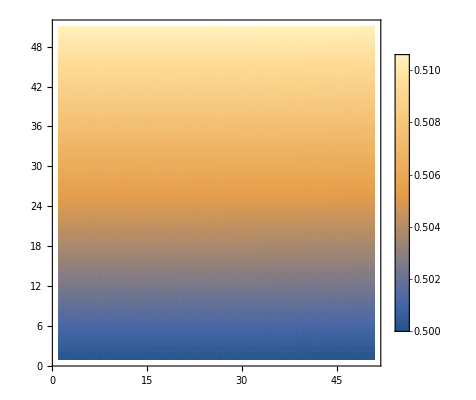

```mathematica
mat1 =ParallelTable[OctavePerlin[x,y,0,3,0.5],{x,0,5,.1},{y,0,5,0.1}];
plot1=ListDensityPlot[mat1,AspectRatio->1,PlotLegends->Automatic]
```

### Marching Cubes

#### Tables

```mathematica
first={0,1,1,2,1,2,2,3,1,2,2,3,2,3,3,2,1,2,2,3,2,3,3,4,2,3,3,4,3,4,4,3,1,2,2,3,2,3,3,4,2,3,3,4,3,4,4,3,2,3,3,2,3,4,4,3,3,4,4,3,4,5,5,2,1,2,2,3,2,3,3,4,2,3,3,4,3,4,4,3,2,3,3,4,3,4,4,5,3,4,4,5,4,5,5,4,2,3,3,4,3,4,2,3,3,4,4,5,4,5,3,2,3,4,4,3,4,5,3,2,4,5,5,4,5,2,4,1,1,2,2,3,2,3,3,4,2,3,3,4,3,4,4,3,2,3,3,4,3,4,4,5,3,2,4,3,4,3,5,2,2,3,3,4,3,4,4,5,3,4,4,5,4,5,5,4,3,4,4,3,4,5,5,4,4,3,5,2,5,4,2,1,2,3,3,4,3,4,4,5,3,4,4,5,2,3,3,2,3,4,4,5,4,5,5,2,4,3,5,4,3,2,4,1,3,4,4,5,4,5,3,4,4,5,5,2,3,4,2,1,2,3,3,2,3,4,2,1,3,2,4,1,2,1,1,0};
second ={
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{0,8,3,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{0,1,9,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,8,3,9,8,1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,2,10,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{0,8,3,1,2,10,-1,-1,-1,-1,-1,-1,-1,-1,-1},{9,2,10,0,2,9,-1,-1,-1,-1,-1,-1,-1,-1,-1},{2,8,3,2,10,8,10,9,8,-1,-1,-1,-1,-1,-1},{3,11,2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{0,11,2,8,11,0,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,9,0,2,3,11,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,11,2,1,9,11,9,8,11,-1,-1,-1,-1,-1,-1},{3,10,1,11,10,3,-1,-1,-1,-1,-1,-1,-1,-1,-1},{0,10,1,0,8,10,8,11,10,-1,-1,-1,-1,-1,-1},{3,9,0,3,11,9,11,10,9,-1,-1,-1,-1,-1,-1},{9,8,10,10,8,11,-1,-1,-1,-1,-1,-1,-1,-1,-1},{4,7,8,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{4,3,0,7,3,4,-1,-1,-1,-1,-1,-1,-1,-1,-1},{0,1,9,8,4,7,-1,-1,-1,-1,-1,-1,-1,-1,-1},{4,1,9,4,7,1,7,3,1,-1,-1,-1,-1,-1,-1},{1,2,10,8,4,7,-1,-1,-1,-1,-1,-1,-1,-1,-1},{3,4,7,3,0,4,1,2,10,-1,-1,-1,-1,-1,-1},{9,2,10,9,0,2,8,4,7,-1,-1,-1,-1,-1,-1},{2,10,9,2,9,7,2,7,3,7,9,4,-1,-1,-1},{8,4,7,3,11,2,-1,-1,-1,-1,-1,-1,-1,-1,-1},{11,4,7,11,2,4,2,0,4,-1,-1,-1,-1,-1,-1},{9,0,1,8,4,7,2,3,11,-1,-1,-1,-1,-1,-1},{4,7,11,9,4,11,9,11,2,9,2,1,-1,-1,-1},{3,10,1,3,11,10,7,8,4,-1,-1,-1,-1,-1,-1},{1,11,10,1,4,11,1,0,4,7,11,4,-1,-1,-1},{4,7,8,9,0,11,9,11,10,11,0,3,-1,-1,-1},{4,7,11,4,11,9,9,11,10,-1,-1,-1,-1,-1,-1},{9,5,4,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{9,5,4,0,8,3,-1,-1,-1,-1,-1,-1,-1,-1,-1},{0,5,4,1,5,0,-1,-1,-1,-1,-1,-1,-1,-1,-1},{8,5,4,8,3,5,3,1,5,-1,-1,-1,-1,-1,-1},{1,2,10,9,5,4,-1,-1,-1,-1,-1,-1,-1,-1,-1},{3,0,8,1,2,10,4,9,5,-1,-1,-1,-1,-1,-1},{5,2,10,5,4,2,4,0,2,-1,-1,-1,-1,-1,-1},{2,10,5,3,2,5,3,5,4,3,4,8,-1,-1,-1},{9,5,4,2,3,11,-1,-1,-1,-1,-1,-1,-1,-1,-1},{0,11,2,0,8,11,4,9,5,-1,-1,-1,-1,-1,-1},{0,5,4,0,1,5,2,3,11,-1,-1,-1,-1,-1,-1},{2,1,5,2,5,8,2,8,11,4,8,5,-1,-1,-1},{10,3,11,10,1,3,9,5,4,-1,-1,-1,-1,-1,-1},{4,9,5,0,8,1,8,10,1,8,11,10,-1,-1,-1},{5,4,0,5,0,11,5,11,10,11,0,3,-1,-1,-1},{5,4,8,5,8,10,10,8,11,-1,-1,-1,-1,-1,-1},{9,7,8,5,7,9,-1,-1,-1,-1,-1,-1,-1,-1,-1},{9,3,0,9,5,3,5,7,3,-1,-1,-1,-1,-1,-1},{0,7,8,0,1,7,1,5,7,-1,-1,-1,-1,-1,-1},{1,5,3,3,5,7,-1,-1,-1,-1,-1,-1,-1,-1,-1},{9,7,8,9,5,7,10,1,2,-1,-1,-1,-1,-1,-1},{10,1,2,9,5,0,5,3,0,5,7,3,-1,-1,-1},{8,0,2,8,2,5,8,5,7,10,5,2,-1,-1,-1},{2,10,5,2,5,3,3,5,7,-1,-1,-1,-1,-1,-1},{7,9,5,7,8,9,3,11,2,-1,-1,-1,-1,-1,-1},{9,5,7,9,7,2,9,2,0,2,7,11,-1,-1,-1},{2,3,11,0,1,8,1,7,8,1,5,7,-1,-1,-1},{11,2,1,11,1,7,7,1,5,-1,-1,-1,-1,-1,-1},{9,5,8,8,5,7,10,1,3,10,3,11,-1,-1,-1},{5,7,0,5,0,9,7,11,0,1,0,10,11,10,0},{11,10,0,11,0,3,10,5,0,8,0,7,5,7,0},{11,10,5,7,11,5,-1,-1,-1,-1,-1,-1,-1,-1,-1},{10,6,5,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{0,8,3,5,10,6,-1,-1,-1,-1,-1,-1,-1,-1,-1},{9,0,1,5,10,6,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,8,3,1,9,8,5,10,6,-1,-1,-1,-1,-1,-1},{1,6,5,2,6,1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,6,5,1,2,6,3,0,8,-1,-1,-1,-1,-1,-1},{9,6,5,9,0,6,0,2,6,-1,-1,-1,-1,-1,-1},{5,9,8,5,8,2,5,2,6,3,2,8,-1,-1,-1},{2,3,11,10,6,5,-1,-1,-1,-1,-1,-1,-1,-1,-1},{11,0,8,11,2,0,10,6,5,-1,-1,-1,-1,-1,-1},{0,1,9,2,3,11,5,10,6,-1,-1,-1,-1,-1,-1},{5,10,6,1,9,2,9,11,2,9,8,11,-1,-1,-1},{6,3,11,6,5,3,5,1,3,-1,-1,-1,-1,-1,-1},{0,8,11,0,11,5,0,5,1,5,11,6,-1,-1,-1},{3,11,6,0,3,6,0,6,5,0,5,9,-1,-1,-1},{6,5,9,6,9,11,11,9,8,-1,-1,-1,-1,-1,-1},{5,10,6,4,7,8,-1,-1,-1,-1,-1,-1,-1,-1,-1},{4,3,0,4,7,3,6,5,10,-1,-1,-1,-1,-1,-1},{1,9,0,5,10,6,8,4,7,-1,-1,-1,-1,-1,-1},{10,6,5,1,9,7,1,7,3,7,9,4,-1,-1,-1},{6,1,2,6,5,1,4,7,8,-1,-1,-1,-1,-1,-1},{1,2,5,5,2,6,3,0,4,3,4,7,-1,-1,-1},{8,4,7,9,0,5,0,6,5,0,2,6,-1,-1,-1},{7,3,9,7,9,4,3,2,9,5,9,6,2,6,9},{3,11,2,7,8,4,10,6,5,-1,-1,-1,-1,-1,-1},{5,10,6,4,7,2,4,2,0,2,7,11,-1,-1,-1},{0,1,9,4,7,8,2,3,11,5,10,6,-1,-1,-1},{9,2,1,9,11,2,9,4,11,7,11,4,5,10,6},{8,4,7,3,11,5,3,5,1,5,11,6,-1,-1,-1},{5,1,11,5,11,6,1,0,11,7,11,4,0,4,11},{0,5,9,0,6,5,0,3,6,11,6,3,8,4,7},{6,5,9,6,9,11,4,7,9,7,11,9,-1,-1,-1},{10,4,9,6,4,10,-1,-1,-1,-1,-1,-1,-1,-1,-1},{4,10,6,4,9,10,0,8,3,-1,-1,-1,-1,-1,-1},{10,0,1,10,6,0,6,4,0,-1,-1,-1,-1,-1,-1},{8,3,1,8,1,6,8,6,4,6,1,10,-1,-1,-1},{1,4,9,1,2,4,2,6,4,-1,-1,-1,-1,-1,-1},{3,0,8,1,2,9,2,4,9,2,6,4,-1,-1,-1},{0,2,4,4,2,6,-1,-1,-1,-1,-1,-1,-1,-1,-1},{8,3,2,8,2,4,4,2,6,-1,-1,-1,-1,-1,-1},{10,4,9,10,6,4,11,2,3,-1,-1,-1,-1,-1,-1},{0,8,2,2,8,11,4,9,10,4,10,6,-1,-1,-1},{3,11,2,0,1,6,0,6,4,6,1,10,-1,-1,-1},{6,4,1,6,1,10,4,8,1,2,1,11,8,11,1},{9,6,4,9,3,6,9,1,3,11,6,3,-1,-1,-1},{8,11,1,8,1,0,11,6,1,9,1,4,6,4,1},{3,11,6,3,6,0,0,6,4,-1,-1,-1,-1,-1,-1},{6,4,8,11,6,8,-1,-1,-1,-1,-1,-1,-1,-1,-1},{7,10,6,7,8,10,8,9,10,-1,-1,-1,-1,-1,-1},{0,7,3,0,10,7,0,9,10,6,7,10,-1,-1,-1},{10,6,7,1,10,7,1,7,8,1,8,0,-1,-1,-1},{10,6,7,10,7,1,1,7,3,-1,-1,-1,-1,-1,-1},{1,2,6,1,6,8,1,8,9,8,6,7,-1,-1,-1},{2,6,9,2,9,1,6,7,9,0,9,3,7,3,9},{7,8,0,7,0,6,6,0,2,-1,-1,-1,-1,-1,-1},{7,3,2,6,7,2,-1,-1,-1,-1,-1,-1,-1,-1,-1},{2,3,11,10,6,8,10,8,9,8,6,7,-1,-1,-1},{2,0,7,2,7,11,0,9,7,6,7,10,9,10,7},{1,8,0,1,7,8,1,10,7,6,7,10,2,3,11},{11,2,1,11,1,7,10,6,1,6,7,1,-1,-1,-1},{8,9,6,8,6,7,9,1,6,11,6,3,1,3,6},{0,9,1,11,6,7,-1,-1,-1,-1,-1,-1,-1,-1,-1},{7,8,0,7,0,6,3,11,0,11,6,0,-1,-1,-1},{7,11,6,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{7,6,11,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{3,0,8,11,7,6,-1,-1,-1,-1,-1,-1,-1,-1,-1},{0,1,9,11,7,6,-1,-1,-1,-1,-1,-1,-1,-1,-1},{8,1,9,8,3,1,11,7,6,-1,-1,-1,-1,-1,-1},{10,1,2,6,11,7,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,2,10,3,0,8,6,11,7,-1,-1,-1,-1,-1,-1},{2,9,0,2,10,9,6,11,7,-1,-1,-1,-1,-1,-1},{6,11,7,2,10,3,10,8,3,10,9,8,-1,-1,-1},{7,2,3,6,2,7,-1,-1,-1,-1,-1,-1,-1,-1,-1},{7,0,8,7,6,0,6,2,0,-1,-1,-1,-1,-1,-1},{2,7,6,2,3,7,0,1,9,-1,-1,-1,-1,-1,-1},{1,6,2,1,8,6,1,9,8,8,7,6,-1,-1,-1},{10,7,6,10,1,7,1,3,7,-1,-1,-1,-1,-1,-1},{10,7,6,1,7,10,1,8,7,1,0,8,-1,-1,-1},{0,3,7,0,7,10,0,10,9,6,10,7,-1,-1,-1},{7,6,10,7,10,8,8,10,9,-1,-1,-1,-1,-1,-1},{6,8,4,11,8,6,-1,-1,-1,-1,-1,-1,-1,-1,-1},{3,6,11,3,0,6,0,4,6,-1,-1,-1,-1,-1,-1},{8,6,11,8,4,6,9,0,1,-1,-1,-1,-1,-1,-1},{9,4,6,9,6,3,9,3,1,11,3,6,-1,-1,-1},{6,8,4,6,11,8,2,10,1,-1,-1,-1,-1,-1,-1},{1,2,10,3,0,11,0,6,11,0,4,6,-1,-1,-1},{4,11,8,4,6,11,0,2,9,2,10,9,-1,-1,-1},{10,9,3,10,3,2,9,4,3,11,3,6,4,6,3},{8,2,3,8,4,2,4,6,2,-1,-1,-1,-1,-1,-1},{0,4,2,4,6,2,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,9,0,2,3,4,2,4,6,4,3,8,-1,-1,-1},{1,9,4,1,4,2,2,4,6,-1,-1,-1,-1,-1,-1},{8,1,3,8,6,1,8,4,6,6,10,1,-1,-1,-1},{10,1,0,10,0,6,6,0,4,-1,-1,-1,-1,-1,-1},{4,6,3,4,3,8,6,10,3,0,3,9,10,9,3},{10,9,4,6,10,4,-1,-1,-1,-1,-1,-1,-1,-1,-1},{4,9,5,7,6,11,-1,-1,-1,-1,-1,-1,-1,-1,-1},{0,8,3,4,9,5,11,7,6,-1,-1,-1,-1,-1,-1},{5,0,1,5,4,0,7,6,11,-1,-1,-1,-1,-1,-1},{11,7,6,8,3,4,3,5,4,3,1,5,-1,-1,-1},{9,5,4,10,1,2,7,6,11,-1,-1,-1,-1,-1,-1},{6,11,7,1,2,10,0,8,3,4,9,5,-1,-1,-1},{7,6,11,5,4,10,4,2,10,4,0,2,-1,-1,-1},{3,4,8,3,5,4,3,2,5,10,5,2,11,7,6},{7,2,3,7,6,2,5,4,9,-1,-1,-1,-1,-1,-1},{9,5,4,0,8,6,0,6,2,6,8,7,-1,-1,-1},{3,6,2,3,7,6,1,5,0,5,4,0,-1,-1,-1},{6,2,8,6,8,7,2,1,8,4,8,5,1,5,8},{9,5,4,10,1,6,1,7,6,1,3,7,-1,-1,-1},{1,6,10,1,7,6,1,0,7,8,7,0,9,5,4},{4,0,10,4,10,5,0,3,10,6,10,7,3,7,10},{7,6,10,7,10,8,5,4,10,4,8,10,-1,-1,-1},{6,9,5,6,11,9,11,8,9,-1,-1,-1,-1,-1,-1},{3,6,11,0,6,3,0,5,6,0,9,5,-1,-1,-1},{0,11,8,0,5,11,0,1,5,5,6,11,-1,-1,-1},{6,11,3,6,3,5,5,3,1,-1,-1,-1,-1,-1,-1},{1,2,10,9,5,11,9,11,8,11,5,6,-1,-1,-1},{0,11,3,0,6,11,0,9,6,5,6,9,1,2,10},{11,8,5,11,5,6,8,0,5,10,5,2,0,2,5},{6,11,3,6,3,5,2,10,3,10,5,3,-1,-1,-1},{5,8,9,5,2,8,5,6,2,3,8,2,-1,-1,-1},{9,5,6,9,6,0,0,6,2,-1,-1,-1,-1,-1,-1},{1,5,8,1,8,0,5,6,8,3,8,2,6,2,8},{1,5,6,2,1,6,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,3,6,1,6,10,3,8,6,5,6,9,8,9,6},{10,1,0,10,0,6,9,5,0,5,6,0,-1,-1,-1},{0,3,8,5,6,10,-1,-1,-1,-1,-1,-1,-1,-1,-1},{10,5,6,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{11,5,10,7,5,11,-1,-1,-1,-1,-1,-1,-1,-1,-1},{11,5,10,11,7,5,8,3,0,-1,-1,-1,-1,-1,-1},{5,11,7,5,10,11,1,9,0,-1,-1,-1,-1,-1,-1},{10,7,5,10,11,7,9,8,1,8,3,1,-1,-1,-1},{11,1,2,11,7,1,7,5,1,-1,-1,-1,-1,-1,-1},{0,8,3,1,2,7,1,7,5,7,2,11,-1,-1,-1},{9,7,5,9,2,7,9,0,2,2,11,7,-1,-1,-1},{7,5,2,7,2,11,5,9,2,3,2,8,9,8,2},{2,5,10,2,3,5,3,7,5,-1,-1,-1,-1,-1,-1},{8,2,0,8,5,2,8,7,5,10,2,5,-1,-1,-1},{9,0,1,5,10,3,5,3,7,3,10,2,-1,-1,-1},{9,8,2,9,2,1,8,7,2,10,2,5,7,5,2},{1,3,5,3,7,5,-1,-1,-1,-1,-1,-1,-1,-1,-1},{0,8,7,0,7,1,1,7,5,-1,-1,-1,-1,-1,-1},{9,0,3,9,3,5,5,3,7,-1,-1,-1,-1,-1,-1},{9,8,7,5,9,7,-1,-1,-1,-1,-1,-1,-1,-1,-1},{5,8,4,5,10,8,10,11,8,-1,-1,-1,-1,-1,-1},{5,0,4,5,11,0,5,10,11,11,3,0,-1,-1,-1},{0,1,9,8,4,10,8,10,11,10,4,5,-1,-1,-1},{10,11,4,10,4,5,11,3,4,9,4,1,3,1,4},{2,5,1,2,8,5,2,11,8,4,5,8,-1,-1,-1},{0,4,11,0,11,3,4,5,11,2,11,1,5,1,11},{0,2,5,0,5,9,2,11,5,4,5,8,11,8,5},{9,4,5,2,11,3,-1,-1,-1,-1,-1,-1,-1,-1,-1},{2,5,10,3,5,2,3,4,5,3,8,4,-1,-1,-1},{5,10,2,5,2,4,4,2,0,-1,-1,-1,-1,-1,-1},{3,10,2,3,5,10,3,8,5,4,5,8,0,1,9},{5,10,2,5,2,4,1,9,2,9,4,2,-1,-1,-1},{8,4,5,8,5,3,3,5,1,-1,-1,-1,-1,-1,-1},{0,4,5,1,0,5,-1,-1,-1,-1,-1,-1,-1,-1,-1},{8,4,5,8,5,3,9,0,5,0,3,5,-1,-1,-1},{9,4,5,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{4,11,7,4,9,11,9,10,11,-1,-1,-1,-1,-1,-1},{0,8,3,4,9,7,9,11,7,9,10,11,-1,-1,-1},{1,10,11,1,11,4,1,4,0,7,4,11,-1,-1,-1},{3,1,4,3,4,8,1,10,4,7,4,11,10,11,4},{4,11,7,9,11,4,9,2,11,9,1,2,-1,-1,-1},{9,7,4,9,11,7,9,1,11,2,11,1,0,8,3},{11,7,4,11,4,2,2,4,0,-1,-1,-1,-1,-1,-1},{11,7,4,11,4,2,8,3,4,3,2,4,-1,-1,-1},{2,9,10,2,7,9,2,3,7,7,4,9,-1,-1,-1},{9,10,7,9,7,4,10,2,7,8,7,0,2,0,7},{3,7,10,3,10,2,7,4,10,1,10,0,4,0,10},{1,10,2,8,7,4,-1,-1,-1,-1,-1,-1,-1,-1,-1},{4,9,1,4,1,7,7,1,3,-1,-1,-1,-1,-1,-1},{4,9,1,4,1,7,0,8,1,8,7,1,-1,-1,-1},{4,0,3,7,4,3,-1,-1,-1,-1,-1,-1,-1,-1,-1},{4,8,7,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{9,10,8,10,11,8,-1,-1,-1,-1,-1,-1,-1,-1,-1},{3,0,9,3,9,11,11,9,10,-1,-1,-1,-1,-1,-1},{0,1,10,0,10,8,8,10,11,-1,-1,-1,-1,-1,-1},{3,1,10,11,3,10,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,2,11,1,11,9,9,11,8,-1,-1,-1,-1,-1,-1},{3,0,9,3,9,11,1,2,9,2,11,9,-1,-1,-1},{0,2,11,8,0,11,-1,-1,-1,-1,-1,-1,-1,-1,-1},{3,2,11,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{2,3,8,2,8,10,10,8,9,-1,-1,-1,-1,-1,-1},{9,10,2,0,9,2,-1,-1,-1,-1,-1,-1,-1,-1,-1},{2,3,8,2,8,10,0,1,8,1,10,8,-1,-1,-1},{1,10,2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,3,8,9,1,8,-1,-1,-1,-1,-1,-1,-1,-1,-1},{0,9,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{0,3,8,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}};
```

#### Marching Cubes

```mathematica
TerrainGenerator[rmax_, samples_,seed_, translation_]  := Module[{Pos, VoxelList, edgeLookup,triangle, formattedSecond, Density,graphicsList, xmax, ymax, zmax, samplesX, samplesY, samplesZ, Δx, Δy,Δz},

SeedRandom[seed];

xmax = rmax[[1]]; samplesX = samples[[1]]; Δx = xmax / (samplesX-1);
ymax = rmax[[2]]; samplesY = samples[[2]]; Δy = ymax / (samplesY-1);
zmax = rmax[[3]];samplesZ = samples[[3]]; Δz = zmax / (samplesZ-1);

(* Vertex Order is v7 ... v0 *)
Pos = {{Δx,0,Δz},{Δx,Δy,Δz},{0,Δy,Δz},{0,0,Δz},{Δx,0,0},{Δx,Δy,0},{0,Δy,0},{0,0,0}}//N;
g[v_] := v + translation;
Pos = Map[g,Pos];

VoxelList = {};
Parallelize[
For[x = 0, x ≤ xmax, x = x +Δx,
For[y = 0, y ≤ ymax, y = y + Δy,
For[z = 0, z ≤zmax, z = z + Δz,
(h[v_]:= v + {x,y,z} ;
VoxelList = Append[VoxelList,Map[h,Pos]];);
];
];
];
]
(* Gives the pair of vertices relevant to the edge 'e' *)
edgeLookup[e_] := edgeLookup[e]= {{0,1},{1,2},{2,3},{3,0},
{4,5},{5,6},{6,7},{7,4},
{4,0},{5,1},{6,2},{7,3}}[[e  + 1]];


(* Linear Interpolation between points
0 == x ( 1 - t ) + y t;
- y / x == 1 / t - 1;
1 / (1 - y / x) == t
x / ( x - y ) == t
 *)
triangle[triplet_] :=(
vertices  = {};
For[temp = 1, temp ≤ Length[triplet], temp = temp + 1,
e = triplet[[temp]];
{p1,p2} = edgeLookup[e];
t =   Density[[9 - (p2+1)]] / ( Density[[9 - (p2+1)]]-Density[[9 - (p1+1) ]] );
v =  t Pos[[9 - (p1+1)]] +  (1 - t )Pos[[9 - (p2+1)]];
vertices = Append[vertices, v];
]; vertices);


formattedSecond[caseNumber_] := formattedSecond[caseNumber]=  
{second[[caseNumber + 1]][[1;;3]],
second[[caseNumber + 1]][[4;;6]],
second[[caseNumber + 1]][[7;;9]],
second[[caseNumber + 1]][[10;;12]],
second[[caseNumber + 1]][[13;;15]]};

graphicsList = {};


Parallelize[
For[i = 1, i ≤ Length[VoxelList], i = i + 1,
Pos = VoxelList[[i]];
Density = Table[f[Pos[[i,1]],Pos[[i,2]],Pos[[i,3]]],{i,1,8}];

binaryCaseNumber = Table[If[Density[[i]] > 0, 1,0],{i,1,Length[Density]}];
caseNumber = Sum[binaryCaseNumber[[i]]2^(8-i),{i,1,8}] ;
polyNumber = first[[caseNumber + 1]];

 (*Max number of polygons in a cube, fixed in Marching Cubes*)
MAXNUMPOLY = 5;

For[j = 1, j <= MAXNUMPOLY, j = j + 1,
quickVec = formattedSecond[caseNumber][[j]];
If[quickVec[[1]] == -1,,
graphicsList = Append[graphicsList,Triangle[triangle[quickVec]]];
];
];
];
];

Graphics3D[graphicsList,BoxRatios->{2,2,1},Boxed->False]
]
```

```mathematica
rmax = {1000,1000,215.};
samples = {50,50,25};
seed = 96;
translation = {-rmax[[1]]/2, -rmax[[2]]/2, 0};
trans2 = {0,0,-75};
(* This is the density function! *)
Clear[f];
f[x_,y_,z_] :=f[x,y,z]= -(Max[0,z]^1.4)+ 6rmax[[3]](OctavePerlin[x,y,z,9,0.35]-0.5) + 0.25;
graphic=TerrainGenerator[rmax, samples,seed, translation+trans2]
```

-Graphics3D-

```mathematica
(*Export["terrain5.obj",graphic]*)
```

terrain5.obj

```mathematica
?Max
```

Max[x_1,x_2,…] yields the numerically largest of the x_i. 
Max[{x_1,x_2,…},{y_1,…},…] yields the largest element of any of the lists.